```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab10\lab10\lab10

```mathematica
res = Import["iteration.txt","List"]
```

{0.110833,0.036574,0.0117899,0.00351821,0.000757536,0.000163839,0.000471348,0.000573979,0.000608232,0.000619664,0.00062348,0.000624753,0.000625178,0.00062532,0.000625367,0.000625383,0.000625388,0.00062539,0.000625391,0.000625391}

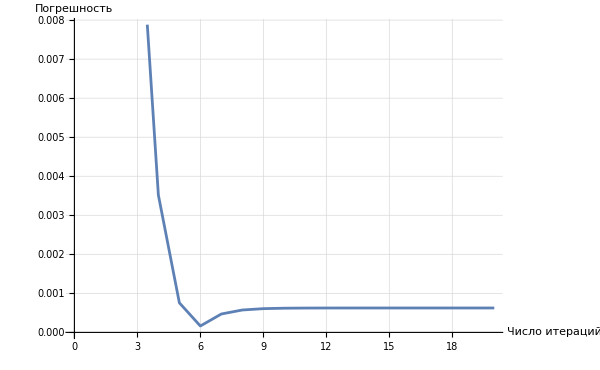

```mathematica
g = ListPlot[res, ImageSize->600,Joined->True,GridLines->Automatic,AxesLabel->{"Число итераций","Погрешность"}]
```

```mathematica
Export["iterationImage.png",g]
```

iterationImage.png